```mathematica
CharTheorem[t_]:=Module[{},
(* get all ordered pairs of a and b s.t. a+b=t *)
abcombos=SortBy[Append[Flatten[Permutations/@IntegerPartitions[t,{2}],1],{t,0}],First];

graphswiththhleqt={};
For[m=1,m≤Length[abcombos],m++, (* loop over all (a,b) pairs *)
(* generate the parent graph K_a □ \overline{K_{b+1}} *)
a=abcombos[[m]][[1]];
b=abcombos[[m]][[2]];
G1=CompleteGraph[a];
G2=GraphComplement[CompleteGraph[b+1]];
graph=GraphComputation`GraphProduct[G1,G2,"Cartesian",VertexLabels->Automatic];
coords=Tuples[{Range[b+1],Range[a]}];
ggrid=Graph[graph,VertexCoordinates->coords,EdgeShapeFunction->"CurvedArc"]; (* formatting the graph *)

(* generate list of all empty pairs *)
emptypairs={};
For[i=1,i≤a,i++,
For[j=1,j≤b,j++,
emptypairs=Append[emptypairs,{i+a*(j-1),i+a*j}]
]
];
emptypairs;

(* generate list of all complete edges *)
completeedges=EdgeList[ggrid];

(* get list of all combinations of empty pairs subsets and complete edges subsets *)
emptypairssubsets=Subsets[emptypairs];
completeedgessubsets=Subsets[completeedges];
EPsAndCEs=Tuples[{emptypairssubsets,completeedgessubsets}];

resultinggraphs={}; (* store graphs that result for each (a,b) pair *)
(* loop over all combinations of empty pairs subsets and complete edges subsets *)
For[i=1,i≤Length[EPsAndCEs],i++,
(* extract list of empty pairs to identify and complete edges to delete *)
emptypairstoidentify=Reverse[EPsAndCEs[[i]][[1]]];
numemptypairs=Length[emptypairstoidentify];
completeedgestodelete=EPsAndCEs[[i]][[2]];

graphfor=EdgeDelete[ggrid,completeedgestodelete]; (* delete the complete edges *)

For[j=1,j≤numemptypairs,j++,
If[
SubsetQ[VertexList[graphfor],emptypairstoidentify[[j]]    ],
graphfor=VertexContract[graphfor,emptypairstoidentify[[j]]   ]  (* identify the empty pairs, if both vertices are still in the graph *)
]
];

numresultinggraphs=Length[resultinggraphs];
isomorphicchecks={};
If[
resultinggraphs=={},  resultinggraphs=Append[resultinggraphs,graphfor], (* if this is the first graph, store it in resultinggraphs *)
For[k=1,k≤numresultinggraphs,k++, (* check if the new graph is isomorphic to any of the previous ones *)
isomorphicchecks=Append[isomorphicchecks,IsomorphicGraphQ[resultinggraphs[[k]],graphfor]]
];
If[ (* store the new graph if it's not isomorphic to any graph before *)
Total[isomorphicchecks]==numresultinggraphs*False,
resultinggraphs=Append[resultinggraphs,graphfor]
]
]
];

(* now, check if any graph in resultinggraphs is isomorphic to any graph generated by a previous (a,b) pair *)
For[l=1,l≤Length[resultinggraphs],l++,
isomorphicchecks2={};
If[
graphswiththhleqt=={},  graphswiththhleqt=Append[graphswiththhleqt,resultinggraphs[[l]]],
For[k=1,k≤Length[graphswiththhleqt],k++,
isomorphicchecks2=Append[isomorphicchecks2,IsomorphicGraphQ[graphswiththhleqt[[k]],resultinggraphs[[l]]]]
];
If[
Total[isomorphicchecks2]==Length[graphswiththhleqt]*False,
graphswiththhleqt=Append[graphswiththhleqt,resultinggraphs[[l]]]
]
]
]
];

(* set the style for each graph in graphswiththhleqt to display it neatly *)
graphswiththhleqtStyle=Table[
Graph[
g,
VertexStyle->White,
VertexSize->.2,
VertexLabels->None,
EdgeStyle->Directive[Black]
],
{g,graphswiththhleqt}];
graphswiththhleqtDisplay=GraphicsGrid[
Partition[graphswiththhleqtStyle,UpTo[10]],
Frame->All
]
]
```

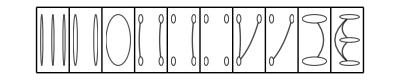

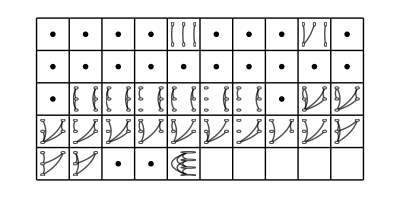

```mathematica
CharTheorem[3]
CharTheorem[4]
```